## Introduction

```mathematica
introvocals=Sound[{
SoundNote["E4",1.75x,"VoiceAahs",SoundVolume->0.7],SoundNote[None,1/4x],SoundNote["E4",1.75x,"VoiceAahs",SoundVolume->0.7],SoundNote[None,1/4x],
SoundNote["D4",4x,"VoiceAahs",SoundVolume->0.7],SoundNote["C#4",1.5x,"VoiceAahs",SoundVolume->0.7],
SoundNote["D4",1/2x,"VoiceAahs",SoundVolume->0.7],SoundNote["C#4",1.75x,"VoiceAahs",SoundVolume->0.7],SoundNote[None,1/4x],SoundNote["B3",4x,"VoiceAahs",SoundVolume->0.7]
}];

introguitarstrum=Sound[{
SoundNote[{"E2","B2","E3"},1.5x,"Guitar"],
SoundNote[{"F#2","C#3","F#3"},1/4x,"Guitar"],SoundNote[{"F#2","C#3","F#3"},1/4x,"Guitar"],
SoundNote[{"F#2","C#3","F#3"},1.5x,"Guitar"],SoundNote[{"G2","D3","G3"},1/4x,"Guitar"],SoundNote[{"G2","D3","G3"},1/4x,"Guitar"],SoundNote[{"G2","D3","G3"},3.5x,"Guitar"],SoundNote[{"A2","E3","A3"},1/4x,"Guitar"],SoundNote[{"A2","E3","A3"},1/4x,"Guitar"],
SoundNote[{"A2","E3","A3"},1.5x,"Guitar"],SoundNote[{"A2","E3","A3"},1/4x,"Guitar"],SoundNote[{"A2","E3","A3"},1/4x,"Guitar"],SoundNote[{"A2","E3","A3"},1.5x,"Guitar"],SoundNote[{"B2","F#3","B3"},1/4x,"Guitar"],SoundNote[{"B2","F#3","B3"},1/4x,"Guitar"],SoundNote[{"B2","F#3","B3"},4x,"Guitar"]
}];

introguitarsingle=Sound[{(* duration: 16x*)
SoundNote["E2",2x,"ElectricGuitar"],SoundNote["F#2",2x,"ElectricGuitar"],SoundNote["G2",4x,"ElectricGuitar"],SoundNote["A2",2x,"ElectricGuitar"],SoundNote["A2",2x,"ElectricGuitar"],SoundNote["B2",4x,"ElectricGuitar"]
}];
surfsup=Sound[{(* duration: 16x *)
Table[SoundNote["B3",1/6x,"ElectricGuitar"],{i,1,6}],Table[SoundNote["G3",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#3",1/6x,"ElectricGuitar"],{i,1,6}],Table[SoundNote["D#3",1/6x,"ElectricGuitar"],{i,1,6}]
}];

mehmehmeh=Sound[{
SoundNote["E5",2x,"Bagpipe"],SoundNote["B4",2x,"Bagpipe"],SoundNote["D5",4x,"Bagpipe"],SoundNote["C#5",1.5x,"Bagpipe"],SoundNote["D5",1/2x,"Bagpipe"],SoundNote["C#5",2x,"Bagpipe"],SoundNote["B4",4x,"Bagpipe"]}];
introfaststrum=Sound[{
Table[SoundNote["E3",1/6x,"ElectricGuitar"],{i,1,10}],SoundNote["D3",1/6x,"ElectricGuitar"],SoundNote["E3",1/6x,"ElectricGuitar"],
Table[SoundNote["F#3",1/6x,"ElectricGuitar"],{i,1,10}],SoundNote["E3",1/6x,"ElectricGuitar"],SoundNote["F#3",1/6x,"ElectricGuitar"],
Table[SoundNote["G3",1/6x,"ElectricGuitar"],{i,1,22}],SoundNote["F#3",1/6x,"ElectricGuitar"],SoundNote["G3",1/6x,"ElectricGuitar"],
Table[SoundNote["A3",1/6x,"ElectricGuitar"],{i,1,4}],Table[SoundNote["G3",1/6x,"ElectricGuitar"],{i,1,4}],Table[SoundNote["F#3",1/6x,"ElectricGuitar"],{i,1,4}],Table[SoundNote["G3",1/6x,"ElectricGuitar"],{i,1,4}],Table[SoundNote["F#3",1/6x,"ElectricGuitar"],{i,1,4}],Table[SoundNote["E3",1/6x,"ElectricGuitar"],{i,1,4}],
Table[SoundNote["D#3",1/6x,"ElectricGuitar"],{i,1,24}]
}];

intropercussion=Sound[{(* Duration: 11.25x *)
Table[SoundNote["LowFloorTom",1/3x,SoundVolume->0.6],{i,1,9}],
SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",x],SoundNote["HighFloorTom",1/4x],SoundNote["HighFloorTom",3/4x],SoundNote["HighFloorTom",1/4x],SoundNote["HighFloorTom",3/4x],SoundNote["HighFloorTom",1/4x],SoundNote["HighFloorTom",1/3x],SoundNote["HighFloorTom",1/3x],SoundNote["HighFloorTom",1/3x]
}];
```

## Riding - Part 1

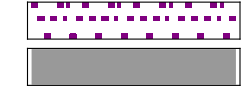

```mathematica
backgroundEm=Sound[{
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"]
}];


gallop=Sound[{
SoundNote["LowTom",1/2x,SoundVolume->0.8],SoundNote["HiHatClosed",1/2x],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x],
SoundNote["LowTom",1/2x],SoundNote["HiHatClosed",1/4x],SoundNote["LowTom",1/4x,SoundVolume->0.8],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x,SoundVolume->0.8],

SoundNote["LowTom",1/2x,SoundVolume->0.8],SoundNote["HiHatClosed",1/2x],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x],
SoundNote["LowTom",1/2x],SoundNote["HiHatClosed",1/4x],SoundNote["LowTom",1/4x,SoundVolume->0.8],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x,SoundVolume->0.8],

SoundNote["LowTom",1/2x,SoundVolume->0.8],SoundNote["HiHatClosed",1/2x],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x],
SoundNote["LowTom",1/2x],SoundNote["HiHatClosed",1/4x],SoundNote["LowTom",1/4x,SoundVolume->0.8],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x,SoundVolume->0.8],

SoundNote["LowTom",1/2x,SoundVolume->0.8],SoundNote["HiHatClosed",1/2x],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x],
SoundNote["LowTom",1/2x],SoundNote["HiHatClosed",1/4x],SoundNote["LowTom",1/4x,SoundVolume->0.8],SoundNote["Snare",1/2x,SoundVolume->0.7],SoundNote["HiHatClosed",1/2x,SoundVolume->0.8]
}];

melodybuzzed=Sound[{
SoundNote["G3",2x,"Sawtooth"],SoundNote["F#3",x,"Sawtooth"],SoundNote["E3",x,"Sawtooth"],
SoundNote["D3",2x,"Sawtooth"],SoundNote["E3",x,"Sawtooth"],SoundNote["F#3",x,"Sawtooth"],
SoundNote["G3",2x,"Sawtooth"],SoundNote["F#3",x,"Sawtooth"],SoundNote["E3",x,"Sawtooth"],
SoundNote["D3",4x,"Sawtooth"],

SoundNote["D#3",2x,"Sawtooth"],SoundNote["E3",x,"Sawtooth"],SoundNote["F#3",x,"Sawtooth"],
SoundNote["E3",2x,"Sawtooth"],SoundNote["G3",x,"Sawtooth"],SoundNote["A3",x,"Sawtooth"],
SoundNote["A#3",2x,"Sawtooth"],SoundNote["A3",x,"Sawtooth"],SoundNote["A#3",x,"Sawtooth"],
SoundNote["B3",4x,"Sawtooth"],

SoundNote["D#4",2x,"Sawtooth"],SoundNote["C4",x,"Sawtooth"],SoundNote["G3",x,"Sawtooth"],SoundNote["D4",4x,"Sawtooth"],
SoundNote["D#4",2x,"Sawtooth"],SoundNote["D4",x,"Sawtooth"],SoundNote["C4",x,"Sawtooth"],SoundNote["A#3",4x,"Sawtooth"],

SoundNote["D4",2x,"Sawtooth"],SoundNote["C4",x,"Sawtooth"],SoundNote["A#3",x,"Sawtooth"],
SoundNote["C4",2x,"Sawtooth"],SoundNote["A#3",x,"Sawtooth"],SoundNote["G#3",x,"Sawtooth"],
SoundNote["A#3",4x,"Sawtooth"],SoundNote["B3",4x,"Sawtooth"]
}];

background1=Sound[{
(* E-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* C-chord *)
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* B-chord *)
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],
(* C-chord *)
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* Cm-chord *)
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* G#-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* G#-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"]
}];

backgroundCm=Sound[{
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"]
}];
```

```mathematica
7.04/.4
```

17.6

## Riding - Part 2

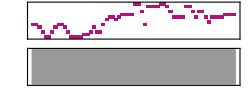

```mathematica
tremelo=Sound[{
Table[SoundNote["D#5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["D5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["C5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["A#4",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["C5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["D5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["D#5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["D5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["C5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["A#4",1/6x,"ElectricGuitar"],{i,1,24}],

Table[SoundNote["B4",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["C5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["D5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["C5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["D#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["F5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["G5",1/6x,"ElectricGuitar"],{i,1,24}],

Table[SoundNote["B5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["G#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["D#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["A#5",1/6x,"ElectricGuitar"],{i,1,24}],
Table[SoundNote["B5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["A#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["G#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,24}],

Table[SoundNote["A#5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["G#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["G#5",1/6x,"ElectricGuitar"],{i,1,12}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["E5",1/6x,"ElectricGuitar"],{i,1,6}],
Table[SoundNote["F#5",1/6x,"ElectricGuitar"],{i,1,24}],
Table[SoundNote["G5",1/6x,"ElectricGuitar"],{i,1,24}]
}]

background2=Sound[{
(* Cm-chord *)
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["Eb3",1/4x,"Square"],SoundNote["C3",1/4x,"Square"],SoundNote["G2",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* G#-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],

(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* G#-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#4",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["F4",1/4x,"Square"],SoundNote["A#4",1/4x,"Square"],SoundNote["F4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],
SoundNote["D#4",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["F4",1/4x,"Square"],SoundNote["A#4",1/4x,"Square"],SoundNote["F4",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],

(* G#-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* E-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* B-chord *)
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],

(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* E-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* B-chord *)
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],
SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["C#3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["F#2",1/4x,"Square"],
(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"]
}];

backgroundAbm=Sound[{(* Duration: 16x *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"]
}];
guitartransition=Sound[{(* Duration: 12x *)
SoundNote["G#5",4x,"ElectricGuitar"],SoundNote[None,1/2x],
SoundNote["B3",1/2x,"Polysynth",SoundVolume->0.6],SoundNote["B3",1/2x,"Polysynth",SoundVolume->0.6],SoundNote["B3",1/2x,"Polysynth",SoundVolume->0.6],SoundNote["B3",3/4x,"Polysynth",SoundVolume->0.6],SoundNote["C#4",1/2x,"Polysynth",SoundVolume->0.6],SoundNote[None,1/4x],SoundNote["C#4",1/2x,"Polysynth",SoundVolume->0.6],SoundNote["C#4",3/4x,"Polysynth",SoundVolume->0.6],SoundNote["B3",3/4x,"Polysynth",SoundVolume->0.6],SoundNote[None,0.1x],SoundNote["A#3",1x,"Polysynth",SoundVolume->0.6],SoundNote["A#3",1.5x,"Polysynth",SoundVolume->0.6]
}];

trumpet=Sound[{(* Duration : 67.5x *)
SoundNote["D#3",1/2x,"Trumpet"],SoundNote["G3",1/2x,"Trumpet"],SoundNote["A#3",1/2x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["D4",2/3x,"Trumpet"],SoundNote["C4",2/3x,"Trumpet"],SoundNote["C4",2x,"Trumpet"],SoundNote[None,2.5x],SoundNote["D#3",1/2x,"Trumpet"],SoundNote["G3",1/2x,"Trumpet"],SoundNote["A#3",1/2x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["D4",2/3x,"Trumpet"],SoundNote["C4",2/3x,"Trumpet"],SoundNote["C4",2x,"Trumpet"],SoundNote[None,2.5x],SoundNote["D#3",1/2x,"Trumpet"],SoundNote["G3",1/2x,"Trumpet"],SoundNote["A#3",1/2x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["D4",2/3x,"Trumpet"],SoundNote["C4",2/3x,"Trumpet"],SoundNote["D4",2x,"Trumpet"],SoundNote[None,2x],SoundNote["C4",1/4x,"Trumpet"],SoundNote["D4",1/4x,"Trumpet"],SoundNote["D#4",2x,"Trumpet"],SoundNote[None,1.5x],SoundNote["F#4",2/3x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["A#3",2/3x,"Trumpet"],SoundNote["G3",2/3x,"Trumpet"],SoundNote["A#3",2/3x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["G4",2/3x,"Trumpet"],SoundNote["D#4",2/3x,"Trumpet"],SoundNote["A#3",2/3x,"Trumpet"],SoundNote["G3",2x,"Trumpet"],
SoundNote["G#4",2x,"Trumpet"],SoundNote[None,2x],SoundNote["D#4",1/4x,"Trumpet"],SoundNote["F4",1/4x,"Trumpet"],SoundNote["G4",2x,"Trumpet"],SoundNote[None,1.5x],SoundNote["G#4",2x,"Trumpet"],SoundNote["F#4",x,"Trumpet"],SoundNote["E4",x,"Trumpet"],
SoundNote["D#4",1/4x,"Trumpet"],SoundNote["E4",1/4x,"Trumpet"],SoundNote["F#4",2x,"Trumpet"],SoundNote[None,1.5x],
SoundNote["G4",2x,"Trumpet"],SoundNote["G#4",x,"Trumpet"],SoundNote["A#4",x,"Trumpet"],SoundNote["G#4",1/4x,"Trumpet"],SoundNote["A#4",1/4x,"Trumpet"],SoundNote["B4",2x,"Trumpet"],SoundNote[None,1.5x],SoundNote["B4",1.5x,"Trumpet"],SoundNote["C#5",1/2x,"Trumpet"],SoundNote["D#5",2/3x,"Trumpet"],SoundNote["C#5",2/3x,"Trumpet"],SoundNote["B4",2/3x,"Trumpet"],
SoundNote["A#4",1.5x,"Trumpet"],SoundNote["A#4",1/4x,"Trumpet"],SoundNote["B4",1/4x,"Trumpet"],SoundNote["C#5",2/3x,"Trumpet"],SoundNote["B4",2/3x,"Trumpet"],SoundNote["A#4",2/3x,"Trumpet"]
}];
```

```mathematica
29.7/.44
```

67.5

```mathematica
x=0.44
```

0.44

## Verse

```mathematica
backgroundverse=Sound[{
(* Abm-chord *)
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
(* E-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],

(* D#-chord *)
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["A#3",1/4x,"Square"],SoundNote["F3",1/4x,"Square"],SoundNote["D#3",1/4x,"Square"],SoundNote["A#2",1/4x,"Square"],
(* E-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G#3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],

(* Em-chord *)
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["E3",1/4x,"Square"],SoundNote["B2",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
(* C-chord *)
SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["G4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],
SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["G4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],

(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
(* C-chord *)
SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["G4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],
SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["G4",1/4x,"Square"],SoundNote["E4",1/4x,"Square"],SoundNote["C4",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],
(* G-chord *)
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["D4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["G3",1/4x,"Square"],SoundNote["D3",1/4x,"Square"],
(* B-chord *)
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],
SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],
SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["F#4",1/4x,"Square"],SoundNote["C#4",1/4x,"Square"],SoundNote["B3",1/4x,"Square"],SoundNote["F#3",1/4x,"Square"]
}];

versevocals=Sound[{
SoundNote["B3",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["A#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["G#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["F#3",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["G#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["A#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["B3",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["A#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["G#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["F#3",4x,"SynthVoice"],
SoundNote["G3",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["G#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["A#3",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["G#3",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["B3",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["C#4",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["D4",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["C#4",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["D4",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["D#4",4x,"SynthVoice"],
SoundNote["G4",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["E4",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["B3",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["F#4",4x,"SynthVoice"],
SoundNote["G4",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["F#4",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["E4",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["D4",4x,"SynthVoice"],
SoundNote["F#4",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["E4",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["D4",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["E4",1.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["D4",0.9x,"SynthVoice"],SoundNote[None,0.1x],SoundNote["C4",0.9x,"SynthVoice"],SoundNote[None,0.1x],
SoundNote["D4",4x,"SynthVoice"],SoundNote["D#4",4x,"SynthVoice"]
}];

verseguitar=Sound[{
SoundNote[{"G#2","D#3","G#3","B3","D#4","G#4"},4x,"Guitar",SoundVolume->0.9],SoundNote[{"B2","F#3","B3","D#4"},4x,"Guitar"],
SoundNote[{"E3","B3","E4","G#4"},4x,"Guitar"],SoundNote[{"B2","F#3","B3","D#4"},4x,"Guitar"],
SoundNote[{"D#3","A#3","D#4","G4"},4x,"Guitar"],SoundNote[{"E3","B3","E4","G#4"},4x,"Guitar"],
SoundNote[{"G2","D3","G3","B3","G4","D4"},4x,"Guitar"],SoundNote[{"B2","F#3","B3","D#4"},4x,"Guitar"],
SoundNote["B4",1/2x,"ElectricGuitar"],SoundNote["G#4",1/2x,"ElectricGuitar"],
SoundNote["E4",3x,"ElectricGuitar"],
SoundNote["B4",1/2x,"ElectricGuitar"],SoundNote["G4",1/2x,"ElectricGuitar"],
SoundNote["D#4",3x,"ElectricGuitar"],
SoundNote["E4",1/4x,"ElectricGuitar"],SoundNote["G#4",1/4x,"ElectricGuitar"],
SoundNote["C5",3.5x,"ElectricGuitar"],
SoundNote[{"D4","G4","B4"},4x,"ElectricGuitar"],
SoundNote[{"D#4","F#4","B4"},4x,"ElectricGuitar"],
SoundNote[{"E4","G4","C4"},4x,"ElectricGuitar"],
SoundNote[{"D4","G4","B4"},4x,"ElectricGuitar"],
SoundNote[{"D#4","F#4","B4"},4x,"ElectricGuitar"]
}];
```

```mathematica
crazydrums=Sound[{
SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",1/2x],
SoundNote["Snare",1/4x],SoundNote["Snare",1/4x],SoundNote["Snare",1/2x],SoundNote["Snare",1/4x],SoundNote["Snare",1/4x],SoundNote["Snare",1/2x],SoundNote["Snare",1/4x],SoundNote["Snare",1/4x],SoundNote["Snare",1/2x],SoundNote["Snare",1/4x],SoundNote["Snare",1/4x],
SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",2x],SoundNote["CrashCymbal",1/2x],
SoundNote["LowTomTom",1/3x],SoundNote["LowTomTom",1/3x],SoundNote["LowTomTom",1/3x],
SoundNote["Snare",1/3x]
}];
```

## Chorus

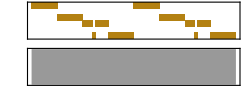

```mathematica
synthtransition=Sound[{
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x]
}];
synthriff=Sound[{
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,2/3x],

SoundNote["D2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["D2",1/3x,"FretlessBass"],
SoundNote["F#2",1/3x,"FretlessBass"],SoundNote["D2",1/3x,"FretlessBass"],SoundNote["F#2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["F#2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["D3",1/3x,"FretlessBass"],SoundNote[None,0.66x],
SoundNote["D2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["D2",1/3x,"FretlessBass"],
SoundNote["F#2",1/3x,"FretlessBass"],SoundNote["D2",1/3x,"FretlessBass"],SoundNote["F#2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["F#2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["D3",1/3x,"FretlessBass"],SoundNote[None,0.66x],

SoundNote["C#2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["C#2",1/3x,"FretlessBass"],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["C#2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["A2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["A2",1/3x,"FretlessBass"],
SoundNote["C#3",1/3x,"FretlessBass"],SoundNote[None,0.66x],
SoundNote["C#2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["C#2",1/3x,"FretlessBass"],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["C#2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["A2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["A2",1/3x,"FretlessBass"],
SoundNote["C#3",1/3x,"FretlessBass"],SoundNote[None,0.66x],

SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,0.66x],
SoundNote["E2",1/3x,"FretlessBass"],SoundNote["B1",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],
SoundNote["G2",1/3x,"FretlessBass"],SoundNote["E2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],
SoundNote["B2",1/3x,"FretlessBass"],SoundNote["G2",1/3x,"FretlessBass"],SoundNote["B2",1/3x,"FretlessBass"],
SoundNote["E3",1/3x,"FretlessBass"],SoundNote[None,0.66x]
}];

chorusvocals=Sound[{
SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],
SoundNote["E4",2x,"SynthVoice"],SoundNote["E4",4/3x,"SynthVoice"],SoundNote["E4",2/3x,"SynthVoice"],
SoundNote["D4",7.5x,"SynthVoice"],SoundNote["D4",1/2x,"SynthVoice"],
SoundNote["C#4",x,"SynthVoice"],SoundNote["C#4",x,"SynthVoice"],SoundNote["C#4",x,"SynthVoice"],SoundNote["B3",x,"SynthVoice"],
SoundNote["C#4",2x,"SynthVoice"],SoundNote["C#4",4/3x,"SynthVoice"],SoundNote["C#4",2/3x,"SynthVoice"],
SoundNote["B3",8x,"SynthVoice"],

SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],SoundNote["E4",x,"SynthVoice"],
SoundNote["E4",2x,"SynthVoice"],SoundNote["E4",4/3x,"SynthVoice"],SoundNote["E4",2/3x,"SynthVoice"],
SoundNote["D4",8x,"SynthVoice"],
SoundNote["C#4",x,"SynthVoice"],SoundNote["C#4",x,"SynthVoice"],SoundNote["C#4",x,"SynthVoice"],SoundNote["B3",x,"SynthVoice"],
SoundNote["C#4",2x,"SynthVoice"],SoundNote["C#4",4/3x,"SynthVoice"],SoundNote["C#4",2/3x,"SynthVoice"],
SoundNote["B3",8x,"SynthVoice"]
}]

chorusvocalshigh=Sound[{
SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],
SoundNote["E5",2x,"SynthVoice"],SoundNote["E5",4/3x,"SynthVoice"],SoundNote["E5",2/3x,"SynthVoice"],
SoundNote["D5",7.5x,"SynthVoice"],SoundNote["D5",1/2x,"SynthVoice"],
SoundNote["C#5",x,"SynthVoice"],SoundNote["C#5",x,"SynthVoice"],SoundNote["C#5",x,"SynthVoice"],SoundNote["B4",x,"SynthVoice"],
SoundNote["C#5",2x,"SynthVoice"],SoundNote["C#5",4/3x,"SynthVoice"],SoundNote["C#5",2/3x,"SynthVoice"],
SoundNote["B4",8x,"SynthVoice"],

SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],SoundNote["E5",x,"SynthVoice"],
SoundNote["E5",2x,"SynthVoice"],SoundNote["E5",4/3x,"SynthVoice"],SoundNote["E5",2/3x,"SynthVoice"],
SoundNote["D5",8x,"SynthVoice"],
SoundNote["C#5",x,"SynthVoice"],SoundNote["C#5",x,"SynthVoice"],SoundNote["C#5",x,"SynthVoice"],SoundNote["B4",x,"SynthVoice"],
SoundNote["C#5",2x,"SynthVoice"],SoundNote["C#5",4/3x,"SynthVoice"],SoundNote["C#5",2/3x,"SynthVoice"],
SoundNote["B4",8x,"SynthVoice"]
}];

guitartriplets=Sound[{
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],

SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],

SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["D5",1/3x,"ElectricGuitar"],

SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["F#4",1/3x,"ElectricGuitar"],
SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["D5",1/3x,"ElectricGuitar"],SoundNote["D5",1/3x,"ElectricGuitar"],

SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["C#5",1/3x,"ElectricGuitar"],

SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["A4",1/3x,"ElectricGuitar"],SoundNote["E4",1/3x,"ElectricGuitar"],
SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["C#5",1/3x,"ElectricGuitar"],SoundNote["C#5",1/3x,"ElectricGuitar"],

SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],

SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["B4",1/3x,"ElectricGuitar"],SoundNote["G4",1/3x,"ElectricGuitar"],
SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"],SoundNote["E5",1/3x,"ElectricGuitar"]
}];
```

```mathematica
bassdrum=Sound[{Table[SoundNote["BassDrum",x],{i,1,16}]}];

risingsnare=Sound[{Table[SoundNote["Snare",1/3x,SoundVolume->i/300],{i,1,187}],
SoundNote["LowTom",1/3x],SoundNote["LowFloorTom",1/3x],SoundNote["CrashCymbal",x]}];
```

```mathematica
27.28/0.44
```

62.

## Riding - Part 3

```mathematica
bestriffever=Sound[{
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",2/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",2/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",2/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["G3",1/3x,"ElectricGuitar"],SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],

SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",2/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",2/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",2/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],

SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",2/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],
SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",2/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],
SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",2/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],
SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["G2",1/3x,"ElectricGuitar"],

SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["A2",2/3x,"ElectricGuitar"]
}];
```

```mathematica
ridingdrums=Sound[{
Table[{SoundNote["BassDrum",x],SoundNote["Snare",x]},{i,1,15}],
SoundNote["Snare",1/3x],SoundNote["LowTom",1/3x],SoundNote["LowFloorTom",1/3x],SoundNote["Snare",x]
}];
ridingdrums2=Sound[{
Table[{SoundNote["BassDrum",x],SoundNote["Snare",x]},{i,1,14}],
Table[SoundNote["LowTom",1/3x],{i,1,9}],SoundNote["Snare",x]}];

ridingcymbals=Sound[{Table[{Table[SoundNote["HiHatOpen",x],{i,1,3}],SoundNote["CrashCymbal",x]},{j,1,7}],
SoundNote["HiHatOpen",x],SoundNote["HiHatOpen",x],
SoundNote[None,4/3x],SoundNote["CrashCymbal",2/3x]}];
echos=Sound[{
SoundNote["E4",4x,"Brightness"],SoundNote["B3",4x,"Brightness"],SoundNote["D4",8x,"Brightness"],
SoundNote["C#4",4x,"Brightness"],SoundNote["B3",2x,"Brightness"],SoundNote["A3",2x,"Brightness"],SoundNote["G3",8x,"Brightness"]
}];
```

```mathematica
14.08/.44
```

32.

## Wrap-Up

```mathematica
riffend=Sound[{
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["A2",1/3x,"ElectricGuitar"],SoundNote["B2",1/3x,"ElectricGuitar"],

SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["G2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],SoundNote["E2",2/3x,"ElectricGuitar"],SoundNote["E2",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],
SoundNote["D3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"],SoundNote["E3",1/3x,"ElectricGuitar"]
}];
```

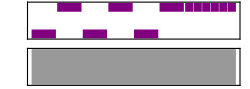

```mathematica
drumriff1=Sound[{
Table[{SoundNote["CrashCymbal",x],Table[SoundNote["Snare",1/3x],{i,1,3}]},{j,1,3}],
Table[SoundNote["LowFloorTom",1/3x],{i,1,6}]
}];
ridecymbal=Sound[{Table[SoundNote["RideCymbal2",2/3x],{i,1,12}]}];
enddrum1=Sound[{
Table[{SoundNote["BassDrum",x],SoundNote["Snare",x]},{i,1,3}],SoundNote["BassDrum",x],Table[SoundNote["Snare",1/3x],{i,1,3}]
}];
enddrum2=Sound[{
Table[{SoundNote["BassDrum",x],SoundNote["Snare",x]},{i,1,3}],Table[SoundNote["Snare",1/3x],{i,1,6}]
}];
```

## Knights

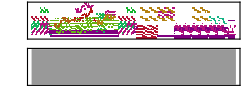

```mathematica
x=0.44;
b=-0x;
knights=Sound[{
(* Introduction *)
Sound[introvocals,{0x+b,16x+b},SoundVolume->0.8],Sound[introguitarstrum,{0x+b,16x+b},SoundVolume->0.7],Sound[introguitarsingle,{0x+b,16x+b}],
Sound[introvocals,{16x+b,32x+b},SoundVolume->0.8],Sound[introguitarstrum,{16x+b,32x+b},SoundVolume->0.7],Sound[introguitarsingle,{16x+b,32x+b}],

Sound[introvocals,{32x+b,48x+b},SoundVolume->0.7],Sound[introguitarstrum,{32x+b,48x+b},SoundVolume->0.7],Sound[introguitarsingle,{32x+b,48x+b}],Sound[mehmehmeh,{32x+b,48x+b},SoundVolume->0.3],Sound[introfaststrum,{32x+b,48x+b}],
Sound[introvocals,{48x+b,64x+b},SoundVolume->1/2],Sound[introguitarstrum,{48x+b,64x+b},SoundVolume->0.7],Sound[introguitarsingle,{48x+b,64x+b}],
Sound[mehmehmeh,{48x+b,64x+b},SoundVolume->0.3],Sound[introfaststrum,{48x+b,64x+b}],
Sound[intropercussion,{53x+b,64.25x+b}],

Sound[surfsup,{64x+b,68x+b}],

(* Riding Music *)
SoundNote["E3",{68x+b,76x+b},"ElectricGuitar"],SoundNote[{"E2","B2"},{68x+b,76x+b},"Guitar"],
Sound[backgroundEm,{68x+b,84x+b},SoundVolume->0.9],Sound[gallop,{68x+b,84x+b}],

Sound[background1,{84x+b,148x+b},SoundVolume->0.8],Sound[melodybuzzed,{84x+b,148x+b},SoundVolume->0.8],
Sound[gallop,{84x+b,100x+b}],Sound[gallop,{100x+b,116x+b}],Sound[gallop,{116x+b,132x+b}],Sound[gallop,{132x+b,148x+b}],
Sound[backgroundCm,{148x+b,164x+b},SoundVolume->0.9],SoundNote["C4",{148x+b,164x+b},"Sawtooth",SoundVolume->0.8],Sound[gallop,{148x+b,164x+b}],

Sound[trumpet,{160.5x+b,228x+b},SoundVolume->1/2],
Sound[background1,{164x+b,228x+b},SoundVolume->0.8],Sound[tremelo,{164x+b,228x+b},SoundVolume->0.8],
Sound[gallop,{164x+b,180x+b}],Sound[gallop,{180x+b,196x+b}],Sound[gallop,{196x+b,212x+b}],Sound[gallop,{212x+b,228x+b}],
Sound[backgroundAbm,{228x+b,244x+b},SoundVolume->0.9],Sound[gallop,{228x+b,244x+b}],Sound[guitartransition,{228x+b,240x+b}],

(* Verse *)
Sound[backgroundverse,{244x+b,308x+b},SoundVolume->0.6],Sound[versevocals,{244x+b,308x+b}],Sound[verseguitar,{244x+b,308x+b},SoundVolume->0.8],
Sound[gallop,{244x+b,260x+b}],Sound[gallop,{260x+b,276x+b}],Sound[gallop,{276x+b,292x+b}],Sound[gallop,{292x+b,308x+b}],
Sound[backgroundEm,{308x+b,324x+b},SoundVolume->0.8],Sound[gallop,{308x+b,324x+b}],SoundNote["E4",{308x+b,312x+b},"SynthVoice"],SoundNote[{"E4","G4","B4"},{308x+b,312x+b},"ElectricGuitar",SoundVolume->0.8],

(* Intro II *)
Sound[introvocals,{324x+b,340x+b},SoundVolume->0.8],Sound[introguitarstrum,{324x+b,340x+b},SoundVolume->0.7],Sound[introguitarsingle,{324x+b,340x+b}],
Sound[introvocals,{340x+b,356x+b},SoundVolume->0.8],Sound[introguitarstrum,{340x+b,356x+b},SoundVolume->0.7],Sound[introguitarsingle,{340x+b,356x+b}],

Sound[introvocals,{356x+b,372x+b},SoundVolume->0.7],Sound[introguitarstrum,{356x+b,372x+b},SoundVolume->0.7],Sound[introguitarsingle,{356x+b,372x+b}],Sound[mehmehmeh,{356x+b,372x+b},SoundVolume->0.3],Sound[introfaststrum,{356x+b,372x+b}],
Sound[introvocals,{372x+b,388x+b},SoundVolume->1/2],Sound[introguitarstrum,{372x+b,388x+b},SoundVolume->0.7],Sound[introguitarsingle,{372x+b,388x+b}],
Sound[mehmehmeh,{372x+b,388x+b},SoundVolume->0.3],Sound[introfaststrum,{372x+b,388x+b}],
Sound[intropercussion,{377x+b,388.25x+b}],

Sound[surfsup,{388x+b,392x+b}],

(* SynthTransition *)
SoundNote["CrashCymbal",{392x+b,396x+b}],
Sound[bassdrum,{392x+b,408x+b},SoundVolume->0.7],Sound[synthtransition,{392x+b,(407+1/3)x+b}],

(* Chorus *)
Sound[chorusvocals,{408x+b,472x+b}],Sound[chorusvocalshigh,{408x+b,472x+b},SoundVolume->0.8],
Sound[synthriff,{408x+b,(439+1/3)x+b},SoundVolume->0.8],Sound[synthriff,{440x+b,(471+1/3)x+b},SoundVolume->0.8],

Sound[chorusvocals,{472x+b,536x+b}],Sound[chorusvocalshigh,{472x+b,536x+b},SoundVolume->0.8],
Sound[guitartriplets,{472x+b,504x+b},SoundVolume->0.6],Sound[guitartriplets,{504x+b,536x+b},SoundVolume->0.6],
Sound[risingsnare,{472x+b,536x+b}],

(* Chorus (Riding thru the Desert) *)
Sound[bestriffever,{536x+b,568x+b}],Sound[ridingdrums,{536x+b,568x+b},SoundVolume->0.7],Sound[ridingcymbals,{536x+b,568x+b},SoundVolume->0.7],
Sound[bestriffever,{568x+b,600x+b}],Sound[ridingdrums2,{568x+b,600x+b},SoundVolume->0.7],Sound[ridingcymbals,{568x+b,600x+b},SoundVolume->0.7],

Sound[chorusvocals,{600x+b,664x+b}],Sound[chorusvocalshigh,{600x+b,664x+b},SoundVolume->0.8],
Sound[bestriffever,{600x+b,632x+b}],Sound[ridingdrums,{600x+b,632x+b},SoundVolume->0.7],Sound[ridingcymbals,{600x+b,632x+b},SoundVolume->0.7],
Sound[bestriffever,{632x+b,664x+b}],Sound[ridingdrums2,{632x+b,664x+b},SoundVolume->0.7],Sound[ridingcymbals,{632x+b,664x+b},SoundVolume->0.7],

Sound[bestriffever,{664x+b,696x+b}],Sound[ridingdrums,{664x+b,696x+b},SoundVolume->0.7],
Sound[ridingcymbals,{664x+b,696x+b},SoundVolume->0.7],
Sound[echos,{664x+b,696x+b},SoundVolume->0.8],
Sound[bestriffever,{696x+b,728x+b}],Sound[ridingdrums2,{696x+b,728x+b},SoundVolume->0.7],Sound[ridingcymbals,{696x+b,728x+b},SoundVolume->0.7],Sound[echos,{696x+b,728x+b},SoundVolume->0.8],

(* Wrap-Up *)
Sound[riffend,{728x+b,744x+b}],Sound[drumriff1,{728x+b,736x+b},SoundVolume->0.7],Sound[enddrum1,{736x+b,744x+b},SoundVolume->0.7],Sound[ridecymbal,{736x+b,744x+b}],
Sound[riffend,{744x+b,760x+b}],Sound[enddrum1,{744x+b,752x+b},SoundVolume->0.7],Sound[ridecymbal,{744x+b,752x+b}],
Sound[enddrum2,{752x+b,760x+b},SoundVolume->0.7],Sound[ridecymbal,{752x+b,760x+b}],

SoundNote[{"E2","E3"},{760x+b,764x+b},"ElectricGuitar"]

}]
```

```mathematica
72+32
```

104